# Coral model: bifurcations

#### Code for Timescale separation in models of symbiosis: state space reduction, multiple attractors and initialization (Pfab et al)

```mathematica
(*parameter values*)
nNH=.18;nNS=.13;nNX=0.2;j0HT=.03;j0ST=.03;σNH=.9;σCH=.1;σNS=.9;σCS=.9;jXm=.13;KX=10^-6;jNm=.035;KN=1.5 10^-6;kCO2=10;jHGm=1;yCL=.1;yC=.8;astar=1.34;kNPQ=112;kROS=80;jCPm=2.8;jSGm=0.25;A1=1.256307;A2=1.385969;A3=6.479055;b=5;X=0;L=30;Ν=1.5*^-6(*attention this is Ν not N; type esc N esc*);
(*functions*)
F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);
jX=(jXm X)/(X+KX);
jN=(jNm Ν)/(Ν+KN);
jHT=j0HT;
rNS=σNS nNS j0ST;
rNH=σNH nNH jHT;
A=A1+A2 E^(-A3 S/H);
(*list of states (fluxes) to track*)
(*format of elements in this list:*)
(*{ variable name, formula (aim for numerical implementation), initial guess (for numerical implementation) } *)  
tsolveall={
jHG->F[jHGm][yC (ρC S/H+jX),(jN+nNX jX+rNH)nNH^-1],
ρN->jN+nNX jX+rNH-nNH jHG,
jeC->jX+ρC S/H-jHG yC^-1,
jCO2->kCO2 jeC,
jL->A L astar,
rCH->σCH(jHT+(1-yC)jHG yC^-1),
rCS->σCS(j0ST+(1-yC)jSG yC^-1),
jCP->F[jCPm][yCL jL,(jCO2+rCH) H/S+rCS](cROS1+1)^-1,
jeL->jL-jCP yCL^-1,
jNPQ->(kNPQ^-1+jeL^-1)^-1,
cROS1->(jeL-jNPQ)/kROS,
jSG->F[jSGm][yC jCP,(ρN H/S+rNS)nNS^-1],
ρC->jCP-jSG yC^-1,
jST->j0ST(1+b cROS1)
};
(*find (fast) equilibria of fluxes*)
(*Clear[findeqs];*)
findeqs[{St_,Ht_}]:=findeqs[{St,Ht}]=Quiet@NSolve[Flatten[{#[[1]]==#[[2]],#[[1]]>=0}&/@tsolveall/.{S->St,H->Ht}],tsolveall[[All,1]],Reals,Method->{"UseSlicingHyperplanes"->False}];
(*choose witch quantities to show*)
toplot={jCP,ρC,ρN,jSG,jHG,jeC,jCO2,rCH,jeL,jNPQ,rCS,cROS1+1,jSG-jST,jHG-jHT,jSG-jST-(jHG-jHT)};
(*labels for plots*)
names={cROS1+1->"c_ROS",jSG-jST-(jHG-jHT)->"S'/S - H'/H",jSG-jST->"S'/S",jHG-jHT->"H'/H",jHG->"\!\(\*SubscriptBox[\(j\), \(HG\)]\)",ρN->"\!\(\*SubscriptBox[\(ρ\), \(N\)]\)",jeC->"\!\(\*SubscriptBox[\(j\), \(eC\)]\)",jCO2->"\!\(\*SubscriptBox[\(j\), SubscriptBox[\(CO\), \(2\)]]\)",jL->"\!\(\*SubscriptBox[\(j\), \(L\)]\)",rCH->"\!\(\*SubscriptBox[\(r\), \(CH\)]\)",rCS->"\!\(\*SubscriptBox[\(r\), \(CS\)]\)",jCP->"\!\(\*SubscriptBox[\(j\), \(CP\)]\)",jeL->"\!\(\*SubscriptBox[\(j\), \(eL\)]\)",jNPQ->"\!\(\*SubscriptBox[\(j\), \(NPQ\)]\)",cROS1->"\!\(\*SubscriptBox[\(c\), \(ROS\)]\)-1",jSG->"\!\(\*SubscriptBox[\(j\), \(SG\)]\)",ρC->"\!\(\*SubscriptBox[\(ρ\), \(C\)]\)",jST->"\!\(\*SubscriptBox[\(j\), \(ST\)]\)"};
(*helper functions*)
sort[list_,var_]:=SortBy[list,(var/.#)&];
fill2[list_,break_]:=Module[{maxlength=Max[Length/@list]},Module[{newlists=Table[{},maxlength]},Table[If[Length[l]≥1,Table[AppendTo[newlists[[Piecewise[{{3, Length[l]==1∧l[[1,1]]>break}, {z, True}}]]],l[[z]]],{z,Length@l}]],{l,list}];newlists]];
sortfindeqs[SH_]:=sort[findeqs[SH],ρC];
break=.4;
fontfamily="Times";
```

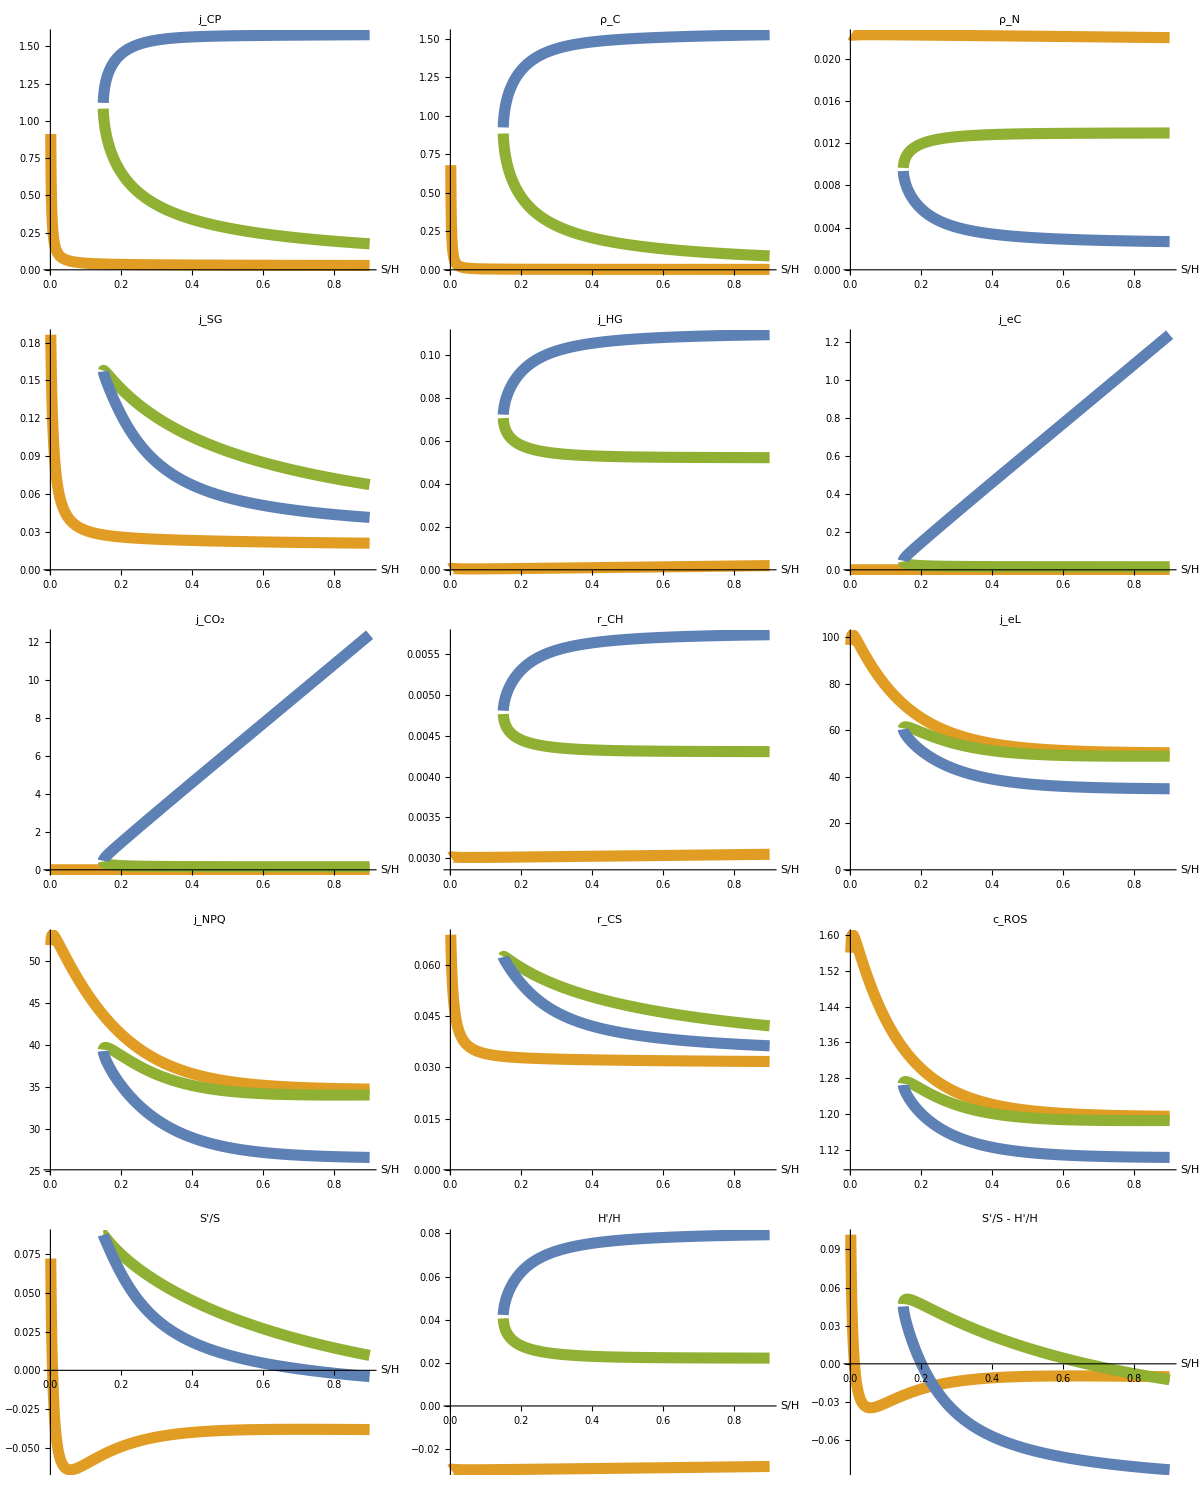

```mathematica
(*range of values for x axis*)
SoverHlist=Join[Range[.001,.145,.001],Range[.1451,.1499,.0001],Range[.15,.55,.002],Range[.56,.9,.01]];
(Export[NotebookDirectory[]<>"coral-bifurcation.pdf",#];#)&@With[{plotlist=Table[ListPlot[fill2[ParallelTable[({SoverH,#}&/@(x/.sortfindeqs[{SoverH,1}])/.{S->SoverH,H->1}),{SoverH,SoverHlist}],break],AxesLabel->{"S/H"},PlotRange->Full,PlotLabel->Style[(x/.names),Italic](*,PlotMarkers->({Graphics`PlotMarkers[][[1,1]],4})*),PlotStyle->Table[{Thickness[.02],ColorData[97][i]},{i,{2,3,1}}],Joined->True(*,AxesOrigin->{0,0}*),LabelStyle->{FontFamily->fontfamily,FontSize->12},ImagePadding->{{37,30},{15,5}}]
,{x,toplot}]},Multicolumn[plotlist,3, Appearance -> "Horizontal",Spacings->0]]
```